# Notebook 20: Functional Programming

## William J Turkel, wturkel@uwo.ca Digital Humanities 1011B

Our textbook defines Functional Programming as “programming where everything is based on evaluating functions and combinations of functions.”  It is the style of programming we have used for this whole course.

## Function application

We have learned a number of different ways to apply functions. The output is the same in every case.

```mathematica
Framed[Reverse[Range[10]]]
```

{10,9,8,7,6,5,4,3,2,1}

```mathematica
Framed@Reverse@Range[10]
```

{10,9,8,7,6,5,4,3,2,1}

```mathematica
Range[10]//Reverse//Framed
```

{10,9,8,7,6,5,4,3,2,1}

```mathematica
Reverse@Range[10] // Framed
```

{10,9,8,7,6,5,4,3,2,1}

In the examples below, make sure you can figure out the order in which the different functions are applied

```mathematica
Framed[Framed[Framed[Framed[Framed[x]]]]]
```

x

```mathematica
Framed@Framed@Framed@Framed@Framed[x]
```

x

```mathematica
Framed@Framed[Framed[x]]//Framed//Framed
```

x

## Pure anonymous functions

### A very simple function

One of the simplest functions that we can define returns its argument unmodified

```mathematica
beYourself[x_]:=
x
```

```mathematica
beYourself[42]
```

42

```mathematica
Map[beYourself,Range[10]]
```

{1,2,3,4,5,6,7,8,9,10}

Here is the pure anonymous version of beYourself applied to the value 42

```mathematica
(# &)[42]
```

42

Here we Map the pure anonymous version of beYourself across a list of the integers from 1 to 10

```mathematica
Map[(# &),Range[10]]
```

{1,2,3,4,5,6,7,8,9,10}

In this case we don’t need the parentheses

```mathematica
Map[# &,Range[10]]
```

{1,2,3,4,5,6,7,8,9,10}

### Another example

```mathematica
plusThree[x_]:=
x+3
```

```mathematica
plusThree[42]
```

45

```mathematica
Map[plusThree,Range[10]]
```

{4,5,6,7,8,9,10,11,12,13}

Here is the pure anonymous version of plusThree applied to the value 42

```mathematica
(#+3&)[42]
```

45

```mathematica
Map[(#+3&),Range[10]]
```

{4,5,6,7,8,9,10,11,12,13}

Again, we don’t need the parentheses for the Map expression

```mathematica
Map[#+3&,Range[10]]
```

### The Select statement

Another use for pure anonymous functions is to set conditions on the Select statement

Pull out even numbers

```mathematica
Select[Range[100],EvenQ]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100}

Pull out numbers that are divisible by 5

```mathematica
Select[Range[100],Mod[#,5]==0&]
```

{5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100}

Pull out numbers that are prime and less than 50

```mathematica
Select[Range[100],#<50&&PrimeQ[#]&]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}

### Pure anonymous functions with more than one argument

Here is an anonymous function to return the least of its two arguments

```mathematica
(If[#1≤#2,#1,#2]&)[4,19]
```

4

```mathematica
(If[#1≤#2,#1,#2]&)[14,9]
```

9

```mathematica
(If[#1≤#2,#1,#2]&)[4,4]
```

4

## Mapping

### Mapping across partitions

Here is a function applied to a list

```mathematica
Framed@Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

Here is the same function mapped across a list

```mathematica
Map[Framed,Range[10]]
```

{1,2,3,4,5,6,7,8,9,10}

You can map across partitioned lists, too

```mathematica
Partition[Range[10],2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
Map[Framed,Partition[Range[10],2]]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

### The Total function

```mathematica
1+2+3+4+5+6+7+8+9+10
```

55

```mathematica
Total[Range[10]]
```

55

```mathematica
Partition[Range[10],2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

Note that Total in this case is applied to each sublist (compare with Framed example above)

```mathematica
Map[Total, Partition[Range[10],2]]
```

{3,7,11,15,19}

### Mapping an anonymous function

Some examples

```mathematica
(Rotate[#,90Degree]&)["Test"]
```

Test

```mathematica
Map[Rotate[#,90Degree]&,Range[10]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Map[Rotate[#,90Degree]&,Partition[Range[10],2]]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

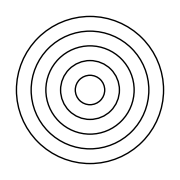

```mathematica
Graphics[Map[Circle[{0,0},#]&,Range[5]],ImageSize->Small]
```

## Nest, NestList and FoldList

Sometimes we want to nest a number of copies of the same function inside one another

```mathematica
Framed[Framed[Framed[Framed[Framed[x]]]]]
```

x

The Nest command does this more efficiently

```mathematica
Nest[Framed,x,5]
```

x

The NestList command performs the same nesting of functions as Nest, but collects each intermediate step as a member of a list.

```mathematica
NestList[Framed, x, 5]
```

{x,x,x,x,x,x}

### Anonymous Functions

An anonymous function blends the color Yellow with its argument

```mathematica
(Blend[{#,Yellow}]&)[Purple]
```

RGBColor[0.75, Rational[1, 2], 0.25]

Starting by blending with Red, we can apply the function a number of times with NestList

```mathematica
NestList[Blend[{#,Yellow}]&,Red,5]
```

{RGBColor[1, 0, 0],RGBColor[1, Rational[1, 2], 0],RGBColor[1, Rational[3, 4], 0],RGBColor[1, Rational[7, 8], 0],RGBColor[1, Rational[15, 16], 0],RGBColor[1, Rational[31, 32], 0]}

If we use an anonymous function to add 2, we can use NestList to create the kind of list we might get with Table

```mathematica
NestList[#+2&,1,5]
```

{1,3,5,7,9,11}

### FoldList

FoldList is a generalization of NestList that works with two arguments. You can often use it when you need to compute a series of terms that depend on previous values.

You can use it to progressively add up numbers. Here is a example using undefined symbols, to show the calculation that will be performed.

```mathematica
FoldList[Plus,0,{a,b,c,d,e}]
```

{0,a,a+b,a+b+c,a+b+c+d,a+b+c+d+e}

When we replace the symbols with integers, we get the running total instead

```mathematica
FoldList[Plus,0,{1,1,1,2,0,0}]
```

{0,1,2,3,5,5,5}

Here is the same computation, using a pure anonymous function

```mathematica
FoldList[#1+#2&,0,{1,1,1,2,0,0}]
```

{0,1,2,3,5,5,5}

Here is an example of using FoldList and Times to compute the first 10 factorials

Factorial[1] = 1
Factorial[2] = 1 x 2 = 2
Factorial[3] = 1 x 2 x 3 = 6 and so on

```mathematica
FoldList[Times,1,Range[10]]
```

{1,1,2,6,24,120,720,5040,40320,362880,3628800}

We can check our work by creating a Table of the first 10 factorials

```mathematica
Table[Factorial[x],{x,1,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

## Iterative and recursive use

### Iterative

The examples of NestList that we have seen so far have been iterative: they consist of a chain of applications of a particular function. Here is a chain of applications of Framed.

```mathematica
NestList[Framed,x,5]
```

{x,x,x,x,x,x}

And a chain of applications of a pure anonymous function that adds two to its argument.

```mathematica
NestList[#+2&,1,5]
```

{1,3,5,7,9,11}

It is more cumbersome than using NestList, but we can write out a sequence of expressions that yield the same output when evaluated.

```mathematica
{x,Framed[x],Framed@Framed[x],Framed@Framed@Framed[x],Framed@Framed@Framed@Framed[x],Framed@Framed@Framed@Framed@Framed[x]}
```

{x,x,x,x,x,x}

### Recursive

It is also possible to use functions like NestList in a more complicated manner. In the example below, nested boxes are combined in twos at each step. This is an example of a recursive use of NestList.

```mathematica
NestList[Framed[Column[{#,#}]]&,x,3]
```

{x,x
x,x
x
x
x,x
x
x
x
x
x
x
x}

When we try to write a sequence of expressions to yield the same output, we discover that the functions are multiply nested inside copies of themselves.

```mathematica
{x, Framed[Column[{x,x}]],Framed[Column[{Framed[Column[{x,x}]],Framed[Column[{x,x}]]}]]}
```

{x,x
x,x
x
x
x}

Try to write the expression for the fourth element of the recursive example of NestList.

### Another recursive example

```mathematica
NestList[Column[{Rotate[#,90Degree],Framed[#]}]&,"Hello",4]
```

{Hello,Hello
Hello,Hello
Hello
Hello
Hello,Hello
Hello
Hello
Hello
Hello
Hello
Hello
Hello,Hello
Hello
Hello
Hello
Hello
Hello
Hello
Hello
Hello
Hello
Hello
Hello
Hello
Hello
Hello
Hello}

## In-Class Activity

### Try creating your own anonymous functions and using them with Map, Nest, NestList, FoldList and Select

#### NAME:

#### STUDENT NUMBER:

#### DATE:

## Upload your notebook

Don’t forget to upload a copy of your notebook for this day’s class to the OWL Site for the course